```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap2D[0.5,1.0];
sizes={64,64};
timeStep=0.001;
k=-0.3;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{64,64} | 2 | 4096 | {7.07107,5.} | {-7.07107,-5.} | {0.224478,0.15873} | {0.437346,0.618501} | {13.9951,19.792}

time | energies | moments | misc
(0) | (total | 0.537868
kinetic | 0.375
potential | 0.375
contact | -0.212132
virial | -0.424264) | (meanX | 0
meanY | 0
sigmaX | 1.
sigmaY | 0.707107
norm | 1.) | (steps | 0
A0 | 0.474383)

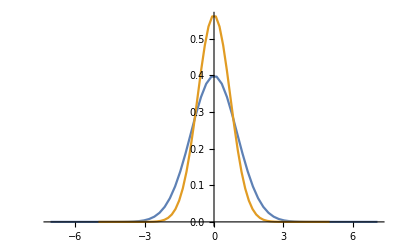

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",30,10]]
```

{24.6819,Null}

time | energies | moments | misc
(30.) | (total | 0.474053
kinetic | 0.623579
potential | 0.237392
contact | -0.386917
virial | -0.0014604) | (meanX | 0
meanY | 0
sigmaX | 0.71277
sigmaY | 0.589723
norm | 1.) | (steps | 30000
A0 | 0.672116)

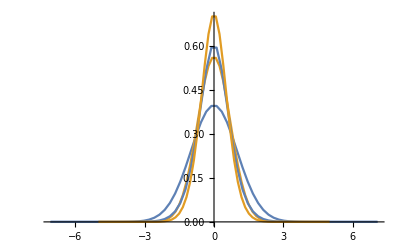

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 0.537868 | 0.375 | 0.375 | -0.212132 | -0.424264
3. | 0.47438 | 0.602869 | 0.244167 | -0.372657 | -0.0279102
6. | 0.474056 | 0.622278 | 0.237804 | -0.386027 | -0.00310541
9. | 0.474053 | 0.6235 | 0.237417 | -0.386863 | -0.0015605
12. | 0.474053 | 0.623574 | 0.237393 | -0.386914 | -0.00146648
15. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.00146077
18. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.00146042
21. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.0014604
24. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.0014604
27. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.0014604
30. | 0.474053 | 0.623579 | 0.237392 | -0.386917 | -0.0014604

```mathematica
reportMoments
```

time | meanX | meanY | sigmaX | sigmaY | norm
0 | 0 | 0 | 1. | 0.707107 | 1.
3. | 0 | 0 | 0.732343 | 0.595192 | 1.
6. | 0 | 0 | 0.713954 | 0.590064 | 1.
9. | 0 | 0 | 0.712842 | 0.589744 | 1.
12. | 0 | 0 | 0.712774 | 0.589724 | 1.
15. | 0 | 0 | 0.71277 | 0.589723 | 1.
18. | 0 | 0 | 0.71277 | 0.589723 | 1.
21. | 0 | 0 | 0.71277 | 0.589723 | 1.
24. | 0 | 0 | 0.71277 | 0.589723 | 1.
27. | 0 | 0 | 0.71277 | 0.589723 | 1.
30. | 0 | 0 | 0.71277 | 0.589723 | 1.